# GWPUser

The GWPTools package provides a robust, object-oriented framework for simulating and analyzing generalized Gaussian wavepackets (GWPs). This user-focused technical note (GWPUser) introduces the front-end capabilities of the software, emphasizing applied quantum mechanics and physical insights rather than backend algorithmic derivations. By using the GWP constructor and interacting with the resulting polymorphic GWPObject, users can rapidly construct analytical wavepacket states, instantly extract exact spatial and momentum representations, and compute advanced energetic observables. This document covers the core 1D wavepacket framework, details rigorous physics extensions like Quantum Hydrodynamics, and previews experimental capabilities—including superposition states and non-unitary open quantum systems.

## Quick-Start Examples

The GWPTools package must first be loaded into the Mathematica session. Assuming the paclet is properly installed on the local filesystem, initialize the framework using the standard Needs command:

Load the GWPTools package.

```mathematica
Needs["GWPTools`"]
```

The core constructor for the package is GWP. By default, calling GWP["1D"][] generates a static, minimum-uncertainty Gaussian wavepacket centered at the origin in phase space. The constructor returns a GWPObject, which acts as the primary data structure for querying physical properties.

Generate the default 1D GWPObject.

```mathematica
gwp=GWP["1D"][]
```

GWPObject[…]

Exact spatial and momentum representations are extracted directly from the GWPObject by passing the appropriate property string. For a static wavepacket, spatial properties evaluate strictly as a function of the position coordinate x.

Evaluate the position-space wavefunction.

```mathematica
gwp["WavefunctionX"][x]
```

(ⅇ^(-x^2/4))/(2 π)^(1/4)

Evaluate the position-space probability density.

```mathematica
gwp["DensityX"][x]
```

(ⅇ^(-x^2/2))/(√(2 π))

A time-dependent wavepacket is created by providing an active external potential using the "Potential" option. The package includes several built-in named potentials, such as the harmonic oscillator ("HO") and the free particle ("Free").

To observe classical oscillatory motion, initial parameters can be passed directly to the GWP constructor. For example, a displaced wavepacket is constructed by passing a real shape parameter (1/2) as the first argument and an initial position offset (1) as the second argument.

Initialize a displaced coherent state in a harmonic oscillator potential.

```mathematica
gwpHO=GWP["1D"][1/2,1,"Potential"->"HO"]
```

GWPObject[…]

Evaluate the time-dependent position expectation value.

```mathematica
gwpHO["PositionExpectation"][t]//Simplify
```

Cos[t]

Evaluate the time-dependent kinetic energy expectation value.

```mathematica
gwpHO["KineticEnergyExpectation"][t]//Simplify
```

1/4 (2-Cos[2 t])

GWPObject natively supports vectorization via list-threading across its coordinate and time arguments. Passing a list of times instantly generates a sequence of evaluated states, facilitating rapid data generation for visualizations.

Plot the spatial probability density at three different times.

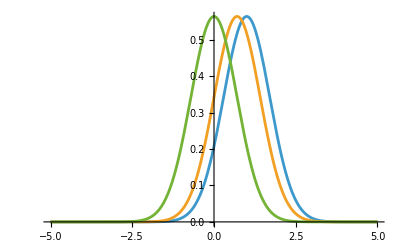

```mathematica
Plot[Evaluate[gwpHO["DensityX"][x,{0,π/4,π/2}]],{x,-5,5}]
```

To explore the framework further, the full list of supported property names for any wavepacket type can be retrieved using the "Properties" introspection query.

Retrieve a list of all supported 1D properties.

```mathematica
GWP["1D"]["Properties"]
```

{Assumptions,ConjugateWavefunctionP,ConjugateWavefunctionX,CumulativeDistributionE,CumulativeDistributionP,CumulativeDistributionX,DensityE,DensityP,DensityX,ExternalForceX,ExternalPotentialX,ForceExpectation,ForceSquaredExpectation,ForceUncertainty,ImaginaryPhase,ImaginaryPhaseTimeDerivative,ImaginaryShape,ImaginaryShapeTimeDerivative,ImaginaryWavefunctionP,ImaginaryWavefunctionX,InitialParameters,InputParameters,KineticEnergyExpectation,KineticEnergyUncertainty,KineticPotentialEnergyCorrelation,KineticPotentialEnergyCovariance,KineticPotentialEnergyProductExpectation,Mass,MomentumCenter,MomentumCenterTimeDerivative,MomentumExpectation,MomentumPositionProductExpectation,MomentumUncertainty,Normalization,PositionCenter,PositionCenterTimeDerivative,PositionExpectation,PositionMomentumCorrelation,PositionMomentumCovariance,PositionMomentumProductExpectation,PositionUncertainty,PotentialCoefficients,PotentialEnergyExpectation,PotentialEnergyUncertainty,PotentialKineticEnergyProductExpectation,ProbabilityE,ProbabilityP,ProbabilityX,RealPhase,RealPhaseTimeDerivative,RealShape,RealShapeTimeDerivative,RealWavefunctionP,RealWavefunctionX,ReducedPlanckConstant,TotalEnergyExpectation,TotalEnergyUncertainty,WavefunctionP,WavefunctionX}

## Mathematical Definitions

### Generalized Complex-Valued Gaussian Wavepacket (GWP)

The notation and parameterization utilized throughout the GWPTools framework are based strictly on the formalism presented in Chapter 3 of David Tannor's Introduction to Quantum Mechanics: A Time-Dependent Perspective.

The mathematical form of a generalized, complex-valued Gaussian wavepacket in one spatial dimension is defined as:

Ψ(x,t)=N ⅇ^(-(α_t(x-x_t))^2+ⅈ/ℏ p_t(x-x_t)+ⅈ/ℏ γ_t)

where  is the spatial coordinate, ℏ is the reduced Planck constant, and the wavepacket is completely characterized by four continuously evolving parameters: , , , and . In this representation,  and  are strictly real-valued quantities, representing the exact center-of-mass position and momentum expectation values.

The complex shape parameter, , completely characterizes the phase-space uncertainty bounds of the state. Its real part  governs the spatial variance, while its imaginary part  dictates the position-momentum correlation, commonly referred to as the momentum "chirp." Similarly, the complex phase parameter  captures the global phase evolution. Its real component accumulates both the classical action and the quantum phase shift induced by wavepacket spreading (analogous to the Gouy phase in optics), while its imaginary component ensures proper time-dependent normalization.

The normalization constant  is purely real-valued and independent of time for quadratic systems, given by:

N =(2/π Re(α_0))^(1/4)ⅇ^(1/ℏ Im(γ_0))

### External Potentials & Time Evolution

The dynamical evolution of the wavepacket is governed by an external potential energy field, $V(x,t)$, which is locally approximated or exactly defined as a polynomial up to second order in the spatial coordinate:

V(x,t)=V_0(t)+V_1(t)x+V_2(t)x^2

A foundational property of this mathematical framework is that any generalized Gaussian wavepacket propagating in a strictly quadratic potential will exactly preserve its Gaussian functional form for all time.

The framework natively supports time-dependent coefficients for the potential. In the current version, explicit time-dependence is comprehensively supported for the external forcing term, , permitting linear and sinusoidal dynamic driving forces. Implementations featuring arbitrary time-dependent shifts to the reference energy  or the harmonic curvature  are designated for future development.

Under this quadratic evolution, the time-dependent wavepacket is continuously characterized by the parameters defined above. These variables (, , , and ) are uniquely determined at any time  by their initial values (, , , and ) and the instantaneous coefficients of the potential energy field. The GWP constructor accepts these initial values as input arguments to instantiate a specific physical state. By querying the resulting dynamic GWPObject, the internal code automatically evaluates these underlying parameters to construct exact time-dependent probabilities, expectation values, and wavefunctions.

### Representations & Observables

A primary advantage of the generalized Gaussian framework is that the wavepacket maintains a closed-form, exact analytical representation across multiple domains. The GWPTools package natively supports the momentum-space representation, evaluating the momentum-space wavefunction  and density  directly from the core parameters without relying on numerical Fourier transforms.

Because the underlying probability densities are Gaussian, exact algebraic solutions exist for the expectation values of physical operators. The internal code utilizes recursive algorithms to analytically evaluate arbitrary-order position moments , momentum moments , and position-momentum cross-products . This permits the exact extraction of higher-order observables—including kinetic, potential, and total energy moments up to the fourth order—completely bypassing the computational overhead and accuracy limits of numerical spatial quadrature.

Finally, integrating the probability densities yields closed-form Cumulative Distribution Functions (CDFs). The package leverages these analytical CDFs to instantly evaluate interval probabilities across position space, momentum space, and the classical energy domain.

## GWP & GWPObject Introspection Interface

The GWPTools package employs a factory pattern for wavepacket construction. As defined by its primary usage statement, GWP[type][parameters, options] returns a GWPObject representing a Gaussian wavepacket with the specified type, parameters, and options. The foundational supported type is "1D", representing a generalized Gaussian wavepacket in one spatial dimension.

List the currently available wavepacket types. Only the "1D" type is available by default.

```mathematica
GWP["Types"]
```

{1D}

The constructor accepts several universal options that dictate the physical constants and environmental landscape. Options such as "MASS" and "HBAR" define the core physical constants, while "Potential" activates a continuous time-evolution model. The "Summary" option controls the visual formatting of the resulting GWPObject.

Construct a time-dependent 1D wavepacket with custom mass and default formatting.

```mathematica
GWP["1D"]["MASS"->2000,"Potential"->"HO","Summary"->Automatic]
```

GWPObject[…]

### The Introspection Framework

The package is entirely self-documenting, eliminating the need to reference static external indices of available functions. The framework's capabilities are accessible via two identical introspection pathways. Queries can be passed directly to the constructor type (e.g., GWP["1D"]) to explore the physics capabilities before instantiating a specific state, or they can be passed directly to a constructed GWPObject.

Physical observables are categorically organized into property classes. The full taxonomy of registered classes can be retrieved using the "Classes" query.

Retrieve a list of all active property classes for the 1D wavepacket type.

```mathematica
GWP["1D"]["Classes"]
```

{DynamicParameters,Energies,ExpectationValues,Probabilities,StaticParameters,Wavefunctions}

To discover specific observables, the general "Properties" query can be filtered by passing the name of a specific class as a secondary argument.

List all properties categorized under the probabilities class.

```mathematica
GWP["1D"]["Properties","Probabilities"]
```

{CumulativeDistributionE,CumulativeDistributionP,CumulativeDistributionX,DensityE,DensityP,DensityX,ProbabilityE,ProbabilityP,ProbabilityX}

Comprehensive metadata regarding how these properties evaluate mathematically can be extracted using the "Records" command. This generates structured datasets mapping each property to its distinct static and dynamic mathematical behaviors.

Extract the detailed metadata records for all properties within the wavefunctions class.

```mathematica
Dataset[GWP["1D"]["Records","Wavefunctions"]]
```

### Mathematical Signatures & State Dynamics

The framework strictly enforces physical consistency through mathematical signatures. The required arguments for querying any physical property depend entirely on whether the wavepacket is initialized as a static or dynamic state.

Static States: When constructed without a dynamic potential (i.e., "Potential" -> None), the wavepacket represents a static, time-independent state. Global properties evaluate instantly as exact constants, while field properties evaluate as pure functions of the spatial coordinate [x].

Dynamic States: Activating an external potential upgrades the mathematical signatures to support continuous time evolution. Global observables automatically shift their signatures to evaluate as temporal functions [t], while field properties expand into bivariate fields over space and time [x, t].

Arbitrary Orders: The framework natively supports higher-order evaluations for analytical wavefunctions, densities, and expectation values. Passing a positive integer argument into the property string specifies either the spatial derivative order or the operator moment.

Instantiate a static and a dynamic wavepacket.

```mathematica
objStatic=GWP["1D"][]
objDynamic=GWP["1D"]["Potential"->"Free"]
```

GWPObject[…]

GWPObject[…]

Evaluate a global property for both states to observe the signature shift.

```mathematica
objStatic["PositionUncertainty"]
objDynamic["PositionUncertainty"][t]
```

1

1/(√(1/(1+t^2/4)))

Evaluate the exact 1st-order spatial derivative of the static and dynamic probability densities.

```mathematica
objStatic["DensityX",1][x]
objDynamic["DensityX",1][x,t]//Simplify
```

-(ⅇ^(-x^2/2) x)/(√(2 π))

-4 ⅇ^(-(2 x^2)/(4+t^2)) √(2/π) (1/(4+t^2))^(3/2) x

### Discovering Potential Models

To model continuous time evolution, the wavepacket must be assigned an external potential. The framework registers exact analytical time-evolution propagators for each wavepacket type. The available models and their exact input templates can be discovered using the "PotentialRecords" query.

Extract the registry of analytical potential models available to the 1D wavepacket type.

```mathematica
Dataset[GWP["1D"]["PotentialRecords"]]
```

## Wavepacket Types: 1D Generalization Gaussian

The "1D" wavepacket type represents a single generalized Gaussian state in one spatial dimension. The GWP constructor accepts up to four positional arguments corresponding to the initial state parameters: the complex shape (), spatial center (), momentum center (), and global phase ().

### Parameter Initialization

The constructor supports variable arity, meaning positional arguments can be omitted from right to left. Any omitted parameter automatically falls back to a standard minimum-uncertainty state centered at the phase-space origin.

Construct wavepackets using default fallbacks, partial initializations, and full explicit parameterization.

```mathematica
OBJ1=GWP["1D"][]
OBJ2=GWP["1D"][1,-2]
OBJ3=GWP["1D"][1,-2,5,π/2]
```

GWPObject[…]

GWPObject[…]

GWPObject[…]

The framework natively supports fully symbolic initialization. By passing undefined variables rather than numerical values, the internal routines generate exact algebraic expressions for all observables. To ensure Mathematica's symbolic simplification engines handle these algebraic expressions efficiently without returning unresolved conditional statements, the GWPObject automatically generates the necessary physical domain constraints via the "Assumptions" property.

Construct a symbolic wavepacket and simplify its position uncertainty using the generated assumptions.

```mathematica
symObj=GWP["1D"][RA+I*IA,RX,RP,RG+I*IG,"HBAR"->HBAR]
assum=symObj["Assumptions"]
Simplify[symObj["PositionUncertainty"],assum]
```

GWPObject[…]

(HBAR|IA|IG|RA|RG|RP|RX)∈ℝ&&RA>0&&HBAR>0

1/(2 √RA)

### Dictionary Injections

Instead of calculating and inputting raw complex parameters manually, users can initialize the wavepacket by injecting specific physical target values using specialized dictionary lists. The constructor automatically parses these dictionaries into the foundational real and imaginary parameter components.

Shape Dictionaries: The complex shape parameter can be defined by targeting a specific spatial uncertainty and covariance using {"Covariance", UX, COVXP}, or by defining the phase-space uncertainty bounds using {"Uncertainty", UX, UP, chirpSign}.

Momentum Dictionaries: The real momentum center can be defined by specifying a target classical kinetic energy and directional sign using {"KineticEnergy", KE, pSign}.

Phase Dictionaries: The global complex phase can be injected using specialized lists such as {"Action", S, MU}, {"Displacement", X0, P0}, {"Coefficient", THETA, AMP}, or {"Evolution", EN, TAU}.

Construct wavepackets using dictionary injections for shape, momentum, and phase.

```mathematica
objShape=GWP["1D"][{"Uncertainty",2,3/2,-1}]
objMom=GWP["1D"][1/4,0,{"KineticEnergy",1,1}]
objPhase=GWP["1D"][1/4,0,Sqrt[2],{"Action",2,1}]
```

GWPObject[…]

GWPObject[…]

GWPObject[…]

### Visualizing Field Dynamics

For dynamic wavepackets, field properties such as wavefunctions and probability densities evaluate as bivariate functions of space and time [x, t]. Because GWPObject natively supports vectorization over its temporal argument, passing a list of times rapidly generates a sequence of evaluated states for visualization.

Initialize a free-particle wavepacket and plot its spatial probability density expanding over time.

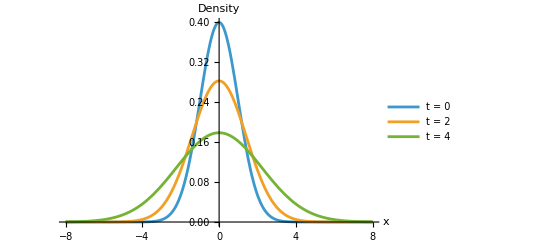

```mathematica
freeObj=GWP["1D"]["Potential"->"Free"];
Plot[Evaluate[freeObj["DensityX"][x,{0,2,4}]],{x,-8,8},PlotRange->All,AxesLabel->{"x","Density"},PlotLegends->{"t = 0","t = 2","t = 4"}]
```

### Tracing Phase Space Trajectories

Global kinematic observables, such as expected position and momentum, evaluate as pure temporal functions [t] when a dynamic potential is active. By evaluating these expectation values as continuous functions of time, exact phase-space trajectories ( vs ) can be traced analytically without numerical differential equation solvers.

Initialize a non-resonant forced harmonic oscillator and trace its phase-space trajectory over multiple driving cycles.

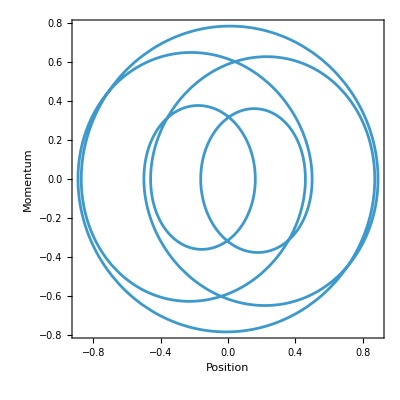

```mathematica
drivenObj=GWP["1D"][1/2,1/2,"Potential"->{"NonResonantForcedHO",1,1/4,6/10}];
ParametricPlot[{
drivenObj["PositionExpectation"][t],
drivenObj["MomentumExpectation"][t]},{t,0,10 π},Frame->True,FrameLabel->{"Position","Momentum"},AspectRatio->1]
```

## Future Directions

While the core "1D" wavepacket type provides a robust foundation for single-state quantum dynamics, the GWPTools framework is architecturally designed to be highly extensible. Several advanced physical models and multi-dimensional state types are currently under active development. Because these modules are experimental, they are not loaded by default and must be explicitly initialized using the Needs command prior to passing their type strings to the GWP constructor.

### Experimental Wavepacket Types

GWP["2D"]—Single Wavepackets in 2D Space:

Extends the generalized Gaussian formalism to two spatial dimensions. This module evaluates 2D potential energy surfaces, coupled coordinate kinematics, and complex momentum-space dynamics.

Initialize the 2D wavepacket type and evaluate the time-dependent spatial density for a free particle.

```mathematica
Needs["GWPTools`GWPEngine2D`"]
GWP["2D"]["Potential"->"Free"]["DensityX"][x,y,t]//Simplify
```

(2 ⅇ^(-(2 (x^2+y^2))/(1+4 t^2)) √(1/((1+4 t^2)^2)))/π

GWP["SS1D"]—Superposition States in 1D Space:

Implements coherent quantum superposition states. By evaluating the off-diagonal cross-density terms between multiple discrete Gaussian wavepackets, this engine exactly resolves transient quantum interference patterns and time-dependent overlap integrals.

Initialize the superposition type and plot the interference pattern of a discrete 1D spatial density.

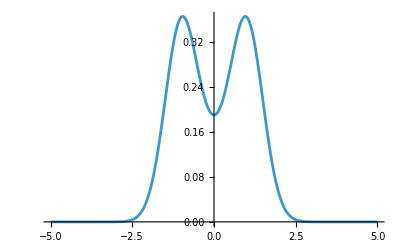

```mathematica
Needs["GWPTools`GWPEngineSS1D`"]
Plot[GWP["SS1D"][]["DensityX"][x],{x,-5,5}]
```

GWP["RDM1D"]—Reduced Density Matrix in 1D Space:

Introduces mixed quantum states and open-system dynamics. This experimental framework expands the GWP formalism into Liouville space to model decoherence, thermal distributions, and environmental coupling.

Initialize the reduced density matrix type and plot the damped spatial trajectory of an open quantum system.

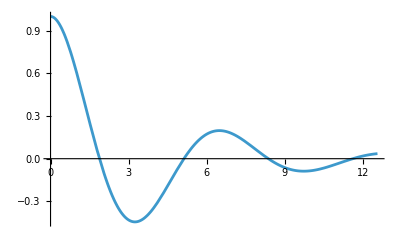

```mathematica
Needs["GWPTools`GWPEngineRDM1D`"]
Plot[GWP["RDM1D"][1/4,1,"Potential"->{"HarmonicCL",1,1/2,1}]["PositionCenter"][t],{t,0,4 Pi}]
```

### Physical Framework Extensions

GWPHydrodynamics:

Expands the package into the domain of quantum hydrodynamics and Bohmian mechanics. This extension natively evaluates probability current densities, exact quantum trajectories, and dynamic quantum potentials derived directly from the underlying parameter bus.

Initialize the hydrodynamics extension, query the available Bohmian observables, and plot the exact quantum trajectories for a harmonic oscillator.

{AmplitudeC,ConvectiveKineticDensityC,CurrentC,DensityC,ExternalForceC,ExternalPotentialC,FisherInformationDensityC,InternalKineticDensityC,MomentumTrajectoryField,OsmoticVelocityC,PhaseC,QuantumForceC,QuantumPotentialC,QuantumStressC,TotalEnergyDensityC,TotalKineticDensityC,TotalPotentialDensityC,TrajectoryField,VelocityC}

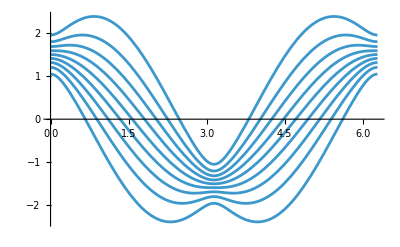

```mathematica
Needs["GWPTools`GWPHydrodynamics`"]
GWP["1D"]["Properties","BohmianTrajectories"]
xc[c_,t_]=GWP["1D"][2,3/2,"Potential"->"HO"]["TrajectoryField"][c,t];
Plot[xc[Range[1/10,9/10,1/10],t],{t,0,2 Pi}]
```

GWPPhaseSpace:

Shifts the analytical focus entirely into the phase-space formulation of quantum mechanics. This module computes exact Wigner quasi-probability distributions and Husimi Q-functions, providing rigorous tools for investigating classical-quantum correspondence and phase-space structures.

Initialize the phase-space extension and evaluate the exact analytical Wigner distribution.

```mathematica
Needs["GWPTools`GWPPhaseSpace`"]
GWP["1D"]["WignerFunction"][x,p]
```

(ⅇ^(-2 p^2-x^2/2))/π

Related Guides

GWPTools

Related Tech Notes

GWPEngine1D

GWPHydrodynamics

GWPPhaseSpace

## Metadata

### Categorization

Tech Note

GWPTools

GWPTools`

GWPTools/tutorial/GWPUser

### Keywords